```mathematica
FileNames["run_001*",{"~/java/e"}]
```

{~/java/e/run_001_001.txt,~/java/e/run_001_002.txt,~/java/e/run_001_003.txt,~/java/e/run_001_004.txt}

```mathematica
readRunData[name_]:=
Module[{allData,noHeaderData,data},
allData = ImportString[Import[name],"TSV"];
noHeaderData = Rest[allData];
data = noHeaderData⟦All,2;;⟧;
{data,noHeaderData⟦All,1⟧, Mean[Transpose[data]], Median[Transpose[data]], Min/@data}
]
```

```mathematica
{data, bsf, avg, med, min}=readRunData["~/java/e/run_001_001.txt"];
```

```mathematica
ListPlot[Transpose[data], PlotRange->All]
```

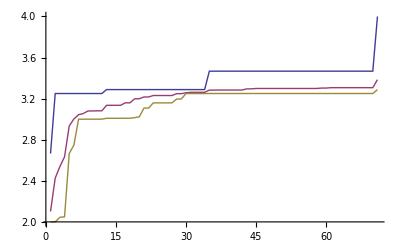

```mathematica
ListLinePlot[{bsf, avg, min}, PlotRange->All]
```

```mathematica
bsfAvg = (readRunData[#]⟦2⟧&/@FileNames["run_001*",{"~/java/e"}]);
```

```mathematica
Max[Length[#]&/@bsfAvg]
```

10000

```mathematica
enlarge[list_]:=list~Join~Array[Max[bsfAvg]&,Max[Length/@bsfAvg]-Length[list]]
```

```mathematica
enlarge[list_]:=list~Join~Array[4,10000-Length[list]]
```

```mathematica
bsfAvg=Mean[(enlarge/@bsfAvg)];
```

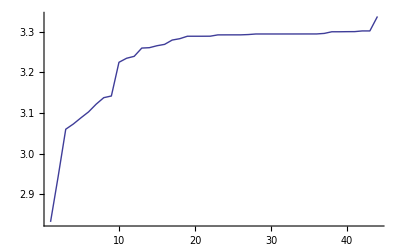

```mathematica
ListLinePlot[{bsfAvg}, PlotRange->All]
```